```mathematica
SetDirectory["C:\Users\jostl\SOLA\5.SEMESTER\Napredna racunalniska orodja\2.DomacaNaloga"];
```

Pribljizek stevila pi:

3.12

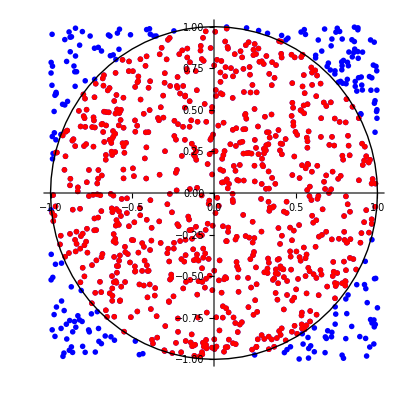

```mathematica
Get["Funkcije1.m"]
aproksimacijaPi[1000]
```

```mathematica
PrimerjavaFunkcij[n_]=
Manipulate[
f[t_]=Sin[t]*t^2*Exp[-t];
ft[t_]=Normal[Series[f[t], {t, 2, u}]];

p1=Plot[f[t], {t, 0, 4}, PlotStyle->Red ];
p2=Plot[ft[t], {t, 0, 4}, PlotStyle->Blue];
Show[p1, p2, AxisLabel->{"t", "f[t], ft[t]"},PlotLabel->"f(t), ft(t)" ]
, {u, 1, n, 1}];
```

```mathematica
PrimerjavaFunkcij[10]
```